## Plane Curves, Singularities and Resolutions

```mathematica
Needs["PlaneCurves`"]
```

## Local Study of Singularities

## Examples

### Double Line

```mathematica
SingularQ[x^2-y^2]
SingularPoints[x^2-y^2]
Map[PointM[x^2-y^2,#]&,SingularPoints[x^2-y^5]]
```

True

{{x→0,y→0}}

{2}

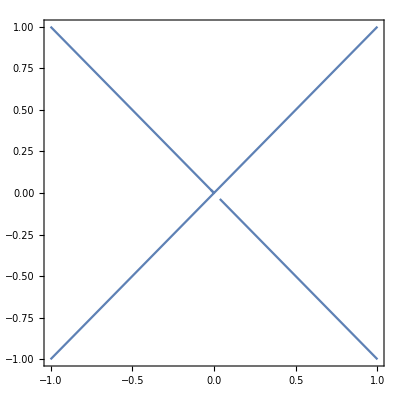

```mathematica
ContourPlot[x^2-y^2==0,{x,-1,1},{y,-1,1}]
```

```mathematica
ResolutionOfSingularities[x^2-y^2]
```

{{{1-v0^2,-1+v1^2},{x→0,y→0}}}

### Cuspidal Cubic

```mathematica
SingularQ[x^2-y^3]
SingularPoints[x^2-y^3]
Map[PointM[x^2-y^3,#]&,SingularPoints[x^2-y^3]]
```

True

{{x→0,y→0}}

{2}

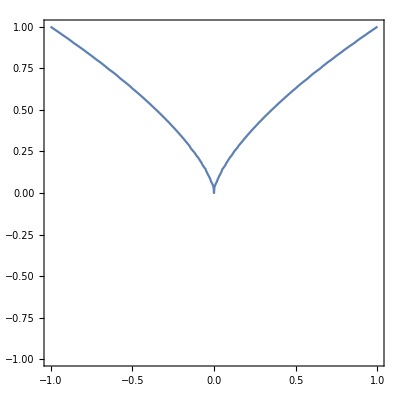

```mathematica
ContourPlot[x^2-y^3==0,{x,-1,1},{y,-1,1}]
```

```mathematica
ResolutionOfSingularities[x^2-y^3]
```

{{{1-u0 v0^3,-u1+v1^2},{x→0,y→0}}}

### Another Example

One singular point of multiplicity 2

```mathematica
SingularQ[x^2-y^5]
SingularPoints[x^2-y^5]
Map[PointM[x^2-y^5,#]&,SingularPoints[x^2-y^5]]
```

True

{{x→0,y→0}}

{2}

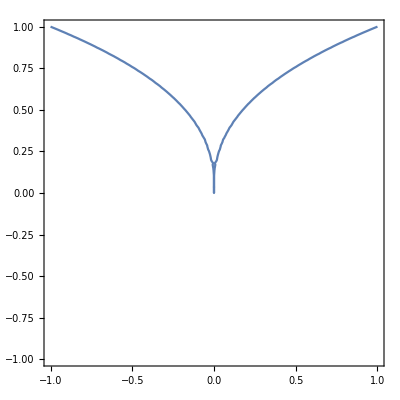

```mathematica
ContourPlot[x^2-y^5==0,{x,-1,1},{y,-1,1}]
```

```mathematica
ResolutionOfSingularities[x^2-y^5]
```

{{{1-u0^3 v0^5,-u10+v10^2,1-u11 v11^3},{x→0,y→0}}}

### A-Polynomial Figure Eight

```mathematica
A41[x_,l_]:=x^2+l^2 x^2+l (-1+x+2 x^2+x^3-x^4)
```

It has two singular points of multiplicity 2

```mathematica
SingularQ[A41[x,l]]
SingularPoints[A41[x,l]]
Map[PointM[A41[x,l],#]&,SingularPoints[A41[x,l]]]
```

True

{{x→-1,l→1},{x→1,l→-1}}

{2,2}

Plot Imaginary parts

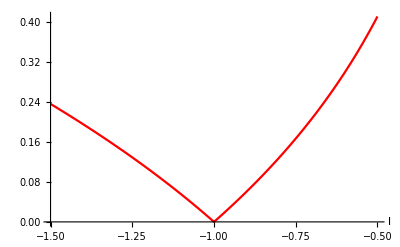

```mathematica
sol[l_]:=FindRoot[A41[x,l],{x,1+0.1*I}][[1,2]]
Plot[(*{Re[sol[l]],*)Im[sol[l]],{l,-0.5,-1.5},AxesLabel->{l,None},PlotLegends->"Expressions",PlotStyle->{Blue,Red}]
```

```mathematica
ResolutionOfSingularities[A41[x,l]]
```

{{{1-2 u0 v0-5 v0^2-5 u0 v0^2+u0^2 v0^2+5 u0 v0^3+5 u0^2 v0^3-u0^2 v0^4-u0^3 v0^4,-5+5 u1-u1^2-5 u1 v1+5 u1^2 v1-u1^3 v1+v1^2-2 u1 v1^2+u1^2 v1^2},{x→-1,l→1}},{{1+2 u0 v0+3 v0^2-3 u0 v0^2+u0^2 v0^2+3 u0 v0^3-3 u0^2 v0^3+u0^2 v0^4-u0^3 v0^4,3+3 u1+u1^2-3 u1 v1-3 u1^2 v1-u1^3 v1+v1^2+2 u1 v1^2+u1^2 v1^2},{x→1,l→-1}}}

```mathematica
NSolve[A41[1,l]==0,l]
```

{{l→-1.},{l→-1.}}

## Global Properties (construction of 1-forms, fundamental differentials...)